```mathematica
Table[{(n-b)/(b)},{n,1,20},{b,1,n}]//Column
```

{{0}}
{{1},{0}}
{{2},{1/2},{0}}
{{3},{1},{1/3},{0}}
{{4},{3/2},{2/3},{1/4},{0}}
{{5},{2},{1},{1/2},{1/5},{0}}
{{6},{5/2},{4/3},{3/4},{2/5},{1/6},{0}}
{{7},{3},{5/3},{1},{3/5},{1/3},{1/7},{0}}
{{8},{7/2},{2},{5/4},{4/5},{1/2},{2/7},{1/8},{0}}
{{9},{4},{7/3},{3/2},{1},{2/3},{3/7},{1/4},{1/9},{0}}
{{10},{9/2},{8/3},{7/4},{6/5},{5/6},{4/7},{3/8},{2/9},{1/10},{0}}
{{11},{5},{3},{2},{7/5},{1},{5/7},{1/2},{1/3},{1/5},{1/11},{0}}
{{12},{11/2},{10/3},{9/4},{8/5},{7/6},{6/7},{5/8},{4/9},{3/10},{2/11},{1/12},{0}}
{{13},{6},{11/3},{5/2},{9/5},{4/3},{1},{3/4},{5/9},{2/5},{3/11},{1/6},{1/13},{0}}
{{14},{13/2},{4},{11/4},{2},{3/2},{8/7},{7/8},{2/3},{1/2},{4/11},{1/4},{2/13},{1/14},{0}}
{{15},{7},{13/3},{3},{11/5},{5/3},{9/7},{1},{7/9},{3/5},{5/11},{1/3},{3/13},{1/7},{1/15},{0}}
{{16},{15/2},{14/3},{13/4},{12/5},{11/6},{10/7},{9/8},{8/9},{7/10},{6/11},{5/12},{4/13},{3/14},{2/15},{1/16},{0}}
{{17},{8},{5},{7/2},{13/5},{2},{11/7},{5/4},{1},{4/5},{7/11},{1/2},{5/13},{2/7},{1/5},{1/8},{1/17},{0}}
{{18},{17/2},{16/3},{15/4},{14/5},{13/6},{12/7},{11/8},{10/9},{9/10},{8/11},{7/12},{6/13},{5/14},{4/15},{3/16},{2/17},{1/18},{0}}
{{19},{9},{17/3},{4},{3},{7/3},{13/7},{3/2},{11/9},{1},{9/11},{2/3},{7/13},{3/7},{1/3},{1/4},{3/17},{1/9},{1/19},{0}}

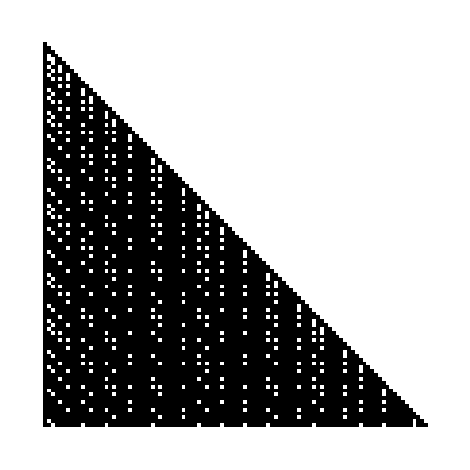

```mathematica
Table[If[PrimeQ[n-b]==True&&PrimeQ[b]==True,0,1],{n,1,100,1},{b,1,n}]//ArrayPlot
```

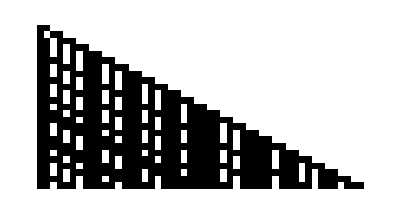

```mathematica
Table[If[PrimeQ[n-b]==True&&PrimeQ[b]==True,0,1],{n,0,50,2},{b,1,n}]//ArrayPlot
```

```mathematica
Table[If[PrimeQ[n-b]==True&&PrimeQ[b]==True,0,1],{n,0,100,2},{b,1,100}]//ArrayPlot
```

-Graphics-

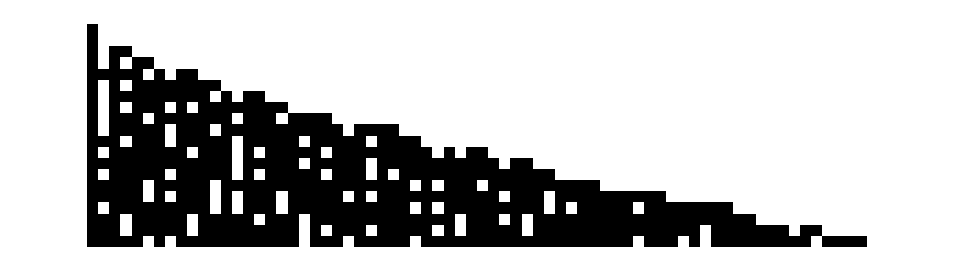

```mathematica
Table[Prime[a]*b+2//PrimeQ//Boole//If[#==0,1,0]&,{a,20},{b,2,Prime[a]}]//ArrayPlot
```